```mathematica
AppendTo[$Path,NotebookDirectory[]<>"../src"];
<<affine.m;
```

```mathematica
externalContour1[axe1_,axe2_,f_formalElement,style_:Dashed,up_:-0.25,left_:0,tcolor_:Black]:={({tcolor,Text[f[#],{#[standardBase][[axe1]],#[standardBase][[axe2]]}]})&/@f[weights],
{style,JoinedCurve[Line[Sort[{#[standardBase][[axe1]],#[standardBase][[axe2]]}&/@f[weights], ArcTan@@#1>ArcTan@@#2&]],CurveClosed->True]}};
```

```mathematica
feplot[axe1_,axe2_,f_formalElement,color_:Blue,up_:-0.25,left_:0]:=
{({color,PointSize[Medium],Point[{#[standardBase][[axe1]],#[standardBase][[axe2]]}]}&)/@f[weights],({color,Text[f[#],{#[standardBase][[axe1]]+left,#[standardBase][[axe2]]+up}]}&)/@f[weights]};
```

```mathematica
splint[al_finiteRootSystem,{rts__?weightQ}]:=(Inverse[Transpose[cartanMatrix[al]]].dynkinLabels[al][#]).{rts}&;
```

```mathematica
onfe[fun_,fe_formalElement]:=makeFormalElement[fun/@fe[weights],fe[multiplicities]];
```

```mathematica
reflection[wg_?weightQ,fe_formalElement]:=makeFormalElement[reflection[wg]/@fe[weights],-fe[multiplicities]];
```

```mathematica
sp=splint[Subscript[A, 2],{makeFiniteWeight[{1,0}],makeFiniteWeight[{0,1}]}];
```

```mathematica
w1=weight[Subscript[B, 2]][3,2]-sp@weight[Subscript[A, 2]][3,2]
```

finiteWeight[2,{4/3,-4/3}]

```mathematica
se=singularElement[makeIrreducibleModule[Subscript[B, 2]][3,2]];
```

```mathematica
se2=singularElement[makeIrreducibleModule[Subscript[A, 2]][3,2]];
```

```mathematica
Graphics[{
externalContour1[2,1,Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]],Dashed,0.25,-0.25],externalContour1[2,1,Exp[-1/2*makeFiniteWeight[{1,-1}]]*reflection[makeFiniteWeight[{1,-1}],(Exp[1/2*makeFiniteWeight[{1,-1}]]*Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])],Dashed,-0.25,0.25],
externalContour1[2,1,se,Dotted,.25,0.25,White],
feplot[2,1,Exp[w1]*onfe[sp,character[makeIrreducibleModule[Subscript[A, 2]][3,2]]],Blue,-0.25,-0.25]},{Frame->True}]
```

-Graphics-

```mathematica
Graphics[{externalContour1[2,1,se,Dotted,.25,0.25,Black],feplot[2,1,character[makeIrreducibleModule[Subscript[B, 2]][3,2]],Blue,-0.25,-0.25]},{Frame->True}]
```

-Graphics-

```mathematica
Graphics[{
externalContour1[2,1,Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]],Dashed,0.25,-0.25],externalContour1[2,1,Exp[-1/2*makeFiniteWeight[{1,-1}]]*reflection[makeFiniteWeight[{1,-1}],(Exp[1/2*makeFiniteWeight[{1,-1}]]*Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])],Dashed,-0.25,0.25],
externalContour1[2,1,se,Dotted,.25,0.25,White],
feplot[2,1,Exp[w1]*onfe[sp,character[makeIrreducibleModule[Subscript[A, 2]][3,2]]],Blue,-0.25,-0.25]},{Frame->True}]
```

```mathematica
drawRoots[axe1_,axe2_,{wgs__?weightQ},color_:Black]:={color,Arrow[{{0,0},{#.axe1,#.axe2}}]}&/@{wgs};
```

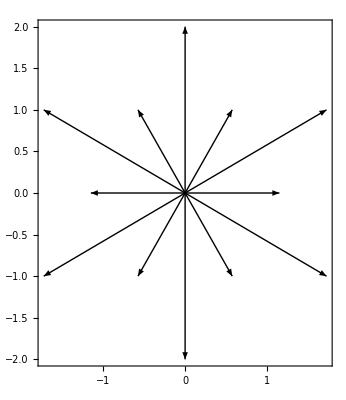

```mathematica
Graphics[drawRoots[ww[[1]],ww[[2]],Union[-positiveRoots[Subscript[G, 2]],positiveRoots[Subscript[G, 2]]]],Frame->True]
```

```mathematica
Needs["ComputationalGeometry`"]
```

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.

```mathematica
ConvexHull[{{1,2},{2,3}}]
```

{1,2}

```mathematica
externalContour2[axe1_,axe2_,f_formalElement,style_:Dashed,up_:-0.25,left_:0,tcolor_:Black]:=
Module[{pts},
pts=({#.axe1,#.axe2}&/@f[weights]);
{({tcolor,Text[f[#],{#.axe1+up,#.axe2+left}]})&/@f[weights],
{style,JoinedCurve[Line[pts[[ConvexHull[pts]]]],CurveClosed->True]}}];
```

```mathematica
a2=makeFiniteRootSystem[{finiteWeight[3,{-2/(√3),1/(√3),1/(√3)}],finiteWeight[3,{1/(√3),-2/(√3),1/(√3)}]}];
```

```mathematica
se3=singularElement[makeIrreducibleModule[a22][3,2]];
```

```mathematica
w2=weight[Subscript[G, 2]][3,2]-weight[a22][3,2];
```

```mathematica
Sequence@@{1,2,3}
```

```mathematica
{2,Sequence[1,2,3]}
```

{2,1,2,3}

```mathematica
cts=Exp[-rho[a2]]*formalOrbit[a2][w2+rho[a2]];
```

```mathematica
Graphics[{drawRoots[ww[[1]],ww[[2]],Sqrt[2]*Union[-positiveRoots[Subscript[G, 2]],positiveRoots[Subscript[G, 2]]]],externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*Exp[rho[Subscript[G, 2]]]*singularElement[makeIrreducibleModule[Subscript[G, 2]][3,2]],Dashed,0.5,0.5],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*Exp[rho[Subscript[G, 2]]]*Exp[w2]*se3,Dotted,-0.5,-0.25],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*reflection[a2[simpleRoot][1],Exp[rho[Subscript[G, 2]]+w2]*se3],Dotted,0.5,-0.25],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*reflection[a2[simpleRoot][2],Exp[rho[Subscript[G, 2]]+w2]*se3],Dotted,0.5,-0.25],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*reflection[a2[simpleRoot][2],reflection[a2[simpleRoot][1],Exp[rho[Subscript[G, 2]]+w2]*se3]],Dotted,-0.5,-0.25],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*reflection[a2[simpleRoot][1],reflection[a2[simpleRoot][2],Exp[rho[Subscript[G, 2]]+w2]*se3]],Dotted,0.25,0.5],
externalContour2[ww[[1]],ww[[2]],Exp[-rho[Subscript[G, 2]]]*reflection[a2[simpleRoot][2],reflection[a2[simpleRoot][1],reflection[a2[simpleRoot][2],Exp[rho[Subscript[G, 2]]+w2]*se3]]],Dotted,0.5,-0.25
],
},Frame->True]
```

-Graphics-

```mathematica
Transpose[Flatten[orbit[a2][#+rho[a2]]]&/@(Exp[w2]*se3)[weights]]
```

Transpose[{{finiteWeight[3,{-√3,-2 √3,3 √3}],finiteWeight[3,{-3 √3,2 √3,√3}],finiteWeight[3,{√3,-3 √3,2 √3}],finiteWeight[3,{-2 √3,3 √3,-√3}],finiteWeight[3,{3 √3,-√3,-2 √3}],finiteWeight[3,{2 √3,√3,-3 √3}]},{finiteWeight[3,{-7/(√3),-2/(√3),3 √3}],finiteWeight[3,{7/(√3),-3 √3,2/(√3)}],finiteWeight[3,{-3 √3,2/(√3),7/(√3)}],finiteWeight[3,{-2/(√3),3 √3,-7/(√3)}],finiteWeight[3,{3 √3,-7/(√3),-2/(√3)}],finiteWeight[3,{2/(√3),7/(√3),-3 √3}]},{finiteWeight[3,{0,-2 √3,2 √3}],finiteWeight[3,{-2 √3,2 √3,0}],finiteWeight[3,{2 √3,0,-2 √3}]},{finiteWeight[3,{-2 √3,-1/(√3),7/(√3)}],finiteWeight[3,{-7/(√3),1/(√3),2 √3}],finiteWeight[3,{2 √3,-7/(√3),1/(√3)}],finiteWeight[3,{-1/(√3),7/(√3),-2 √3}],finiteWeight[3,{7/(√3),-2 √3,-1/(√3)}],finiteWeight[3,{1/(√3),2 √3,-7/(√3)}]},{finiteWeight[3,{0,-2/(√3),2/(√3)}],finiteWeight[3,{-2/(√3),2/(√3),0}],finiteWeight[3,{2/(√3),0,-2/(√3)}]},{finiteWeight[3,{-2/(√3),-1/(√3),√3}],finiteWeight[3,{2/(√3),-√3,1/(√3)}],finiteWeight[3,{-√3,1/(√3),2/(√3)}],finiteWeight[3,{-1/(√3),√3,-2/(√3)}],finiteWeight[3,{√3,-2/(√3),-1/(√3)}],finiteWeight[3,{1/(√3),2/(√3),-√3}]}}]

```mathematica
-rho[a2]]*reflection[a2[simpleRoot][1],Exp[w2+rho[a2]]*se3]
```

```mathematica
Sequence@@(externalContour2[ww[[1]],ww[[2]],Exp[#]*se3,Dotted]&/@cts[weights]),
```

```mathematica
Graphics[externalContour2[ww[[1]],ww[[2]],Exp[-rho[a2]]*orbit[a2][Exp[w2+rho[a2]]*se3],Dashed,0.25,-0.25]]
```

-Graphics-

```mathematica
Graphics[externalContour2[ww[[1]],ww[[2]],orbit[a22][Exp[w2]*se3]]]
```

-Graphics-

```mathematica
w2=weight[Subscript[G, 2]][3,2]-weight[a22][2,1];
```

finiteWeight[3,{-1/(√3),-2/(√3),√3}]

```mathematica
a22=makeFiniteRootSystem[{finiteWeight[3,{1/(√3),-1/(√3),0}],finiteWeight[3,{-1/(√3),0,1/(√3)}]}];
```

```mathematica
formalOrbit[a22][w2]
```

formalElement[Affine`Private`table$3808]

```mathematica
positiveRoots[Subscript[G, 2]]
```

{finiteWeight[3,{1/(√3),-1/(√3),0}],finiteWeight[3,{-2/(√3),1/(√3),1/(√3)}],finiteWeight[3,{1/(√3),-2/(√3),1/(√3)}],finiteWeight[3,{-1/(√3),0,1/(√3)}],finiteWeight[3,{0,-1/(√3),1/(√3)}],finiteWeight[3,{-1/(√3),-1/(√3),2/(√3)}]}

```mathematica
sp2=splint[Subscript[A, 2],{finiteWeight[3,{-2/(√3),1/(√3),1/(√3)}],finiteWeight[3,{1/(√3),-2/(√3),1/(√3)}]}];
```

```mathematica
Subscript[G, 2][simpleRoots]
```

{finiteWeight[3,{1/(√3),-1/(√3),0}],finiteWeight[3,{-2/(√3),1/(√3),1/(√3)}]}

```mathematica
ww.ww
```

finiteWeight[3,{1,-1,0}]^2+finiteWeight[3,{-1/(√3),-1/(√3),2/(√3)}]^2

```mathematica
ww={makeFiniteWeight[{1,-1,0}],makeFiniteWeight[2/Sqrt[3]*(3/2*{1,-1,0}+{-2,1,1})]}
```

{finiteWeight[3,{1,-1,0}],finiteWeight[3,{-1/(√3),-1/(√3),2/(√3)}]}

```mathematica
1,-1,0
```

```mathematica
2/Sqrt[3]*(3/2*{1,-1,0}+{-2,1,1})
```

{-1/(√3),-1/(√3),2/(√3)}

```mathematica
{-1/(√3),-1/(√3),2/(√3)}
```

```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive which represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

```mathematica
?Line
```

Line[{pt_1,pt_2,…}] is a graphics primitive which represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.

```mathematica
b2=Subscript[B, 2];
```

```mathematica
m=makeIrreducibleModule[b2][3,2];
```

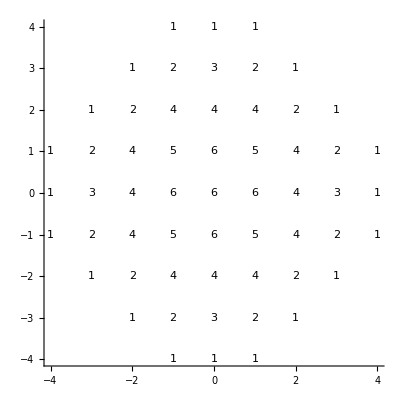

```mathematica
textPlot[m,{Axes->True}]
```

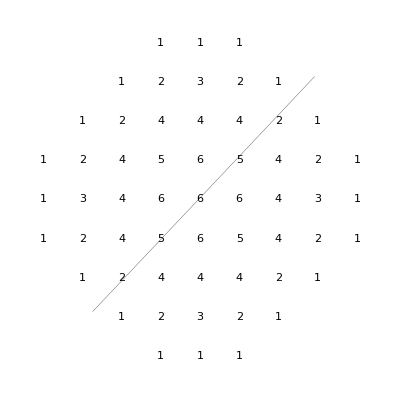

```mathematica
se=singularElement[m];
```

```mathematica
se
```

formalElement[Affine`Private`table$1278]

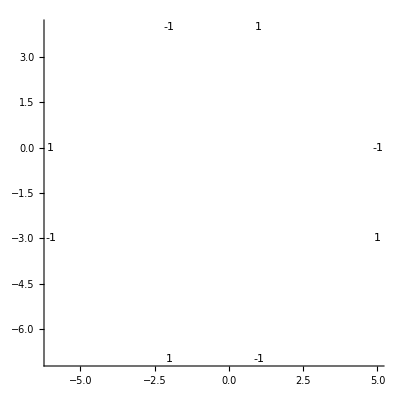

```mathematica
drawPlaneProjection[2,1,se,{Axes->True}]
```

```mathematica
externalContour[axe1_,axe2_,f_formalElement,style_:Dashed,opts___?OptionQ]:=Graphics[
{(Text[f[#],{#[standardBase][[axe1]],#[standardBase][[axe2]]-0.25}])&/@f[weights],
{style,JoinedCurve[Line[Sort[{#[standardBase][[axe1]],#[standardBase][[axe2]]}&/@f[weights], ArcTan@@#1>ArcTan@@#2&]],CurveClosed->True]}},opts]
```

```mathematica
externalContour1[axe1_,axe2_,f_formalElement,style_:Dashed]:={(Text[f[#],{#[standardBase][[axe1]],#[standardBase][[axe2]]-0.25}])&/@f[weights],
{style,JoinedCurve[Line[Sort[{#[standardBase][[axe1]],#[standardBase][[axe2]]}&/@f[weights], ArcTan@@#1>ArcTan@@#2&]],CurveClosed->True]}}
```

```mathematica
Sort[{#[standardBase][[1]],#[standardBase][[2]]}&/@se[weights], ArcTan@@#1>ArcTan@@#2&]
```

{{-7,-2},{-3,-6},{0,-6},{4,-2},{4,1},{0,5},{-3,5},{-7,1}}

```mathematica
externalContour[axe1_,axe2_,f_formalElement,style_:Dashed,opts___?OptionQ]:=Graphics[
(Text[{f[#],#[standardBase][[axe1]],#[standardBase][[axe2]]}])&/@f[weights]];
```

```mathematica
externalContour[2,1,se,Dotted,Axes->True]
```

externalContour[2,1,se,Dashing[{0,Small}],Axes→True]

```mathematica
Inverse[Transpose[cartanMatrix[b2]]]
```

{{1,1},{1/2,1}}

```mathematica
splint[al_finiteRootSystem,{rts__?weightQ}]:=(Inverse[Transpose[cartanMatrix[al]]].dynkinLabels[al][#]).{rts}&;
```

```mathematica
splint[Subscript[A, 2],{makeFiniteWeight[{1,0}],makeFiniteWeight[{0,1}]}]@weight[Subscript[A, 2]][1,0]
```

finiteWeight[2,{2/3,1/3}]

```mathematica
se2=singularElement[makeIrreducibleModule[Subscript[A, 2]][3,2]]
```

formalElement[Affine`Private`table$884]

```mathematica
sp=splint[Subscript[A, 2],{makeFiniteWeight[{1,0}],makeFiniteWeight[{0,1}]}];
```

```mathematica
sp@weight[Subscript[A, 2]][3,2]
```

finiteWeight[2,{8/3,7/3}]

```mathematica
w1=weight[Subscript[B, 2]][3,2]-sp@weight[Subscript[A, 2]][3,2]
```

finiteWeight[2,{4/3,-4/3}]

```mathematica
sp/@se2[weights]
```

```mathematica
sp@rho[Subscript[A, 2]]
```

finiteWeight[2,{1,1}]

```mathematica
(Exp[weight[Subscript[B, 2]][1,-1]]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])[weights]
```

{finiteWeight[2,{17/6,13/6}],finiteWeight[2,{-1/6,13/6}],finiteWeight[2,{17/6,-11/6}],finiteWeight[2,{-25/6,-11/6}],finiteWeight[2,{-1/6,-29/6}],finiteWeight[2,{-25/6,-29/6}]}

```mathematica
reflection[wg_?weightQ,fe_formalElement]:=makeFormalElement[reflection[wg]/@fe[weights],-fe[multiplicities]];
```

```mathematica
Graphics[{externalContour1[2,1,Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]],Dashed],externalContour1[2,1,Exp[-1/2*makeFiniteWeight[{1,-1}]]*reflection[makeFiniteWeight[{1,-1}],(Exp[1/2*makeFiniteWeight[{1,-1}]]*Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])],Thick],
externalContour1[2,1,se,Dotted]},Axes->True]
```

-Graphics-

```mathematica
fe2=(Exp[1/2*makeFiniteWeight[{1,-1}]]*Exp[w1]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])
```

formalElement[Affine`Private`table$993]

```mathematica
reflection[makeFiniteWeight[{1,-1}],fe2]
```

formalElement[Affine`Private`table$998]

```mathematica
{{2,-2},{-1,2}}
```

```mathematica
externalContour[2,1,singularElement[makeIrreducibleModule[Subscript[B, 2]][0,1]],Dotted,Axes->True]
```

-Graphics-

```mathematica
simpleRoots[b2]
```

{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}

```mathematica
fundamentalWeights[b2]
```

{finiteWeight[2,{1,0}],finiteWeight[2,{1/2,1/2}]}

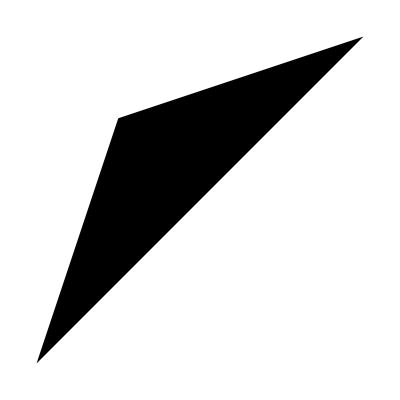

```mathematica
Graphics[Polygon[{{1,1},{2,2},{-1,1},{-2,-2}}]]
```

```mathematica
?Polygon
```

Polygon[{pt_1,pt_2,…}] is a graphics primitive that represents a filled polygon. 
Polygon[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of polygons.

```mathematica
?Line
```

Line[{pt_1,pt_2,…}] is a graphics primitive which represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.